# © Kamal K. Barley, Andreas Ruffing, and Sergei K. Suslov “Oganesson versus Uranium Hydrogen-like Ions from the Viewpoint of Old Quantum Mechanics”

arXiv:2509.06249v2 [quant-ph] 11 Sept 2025

https://arxiv.org/pdf/2509.06249

(Last modified/executed on September  24, 2025;  19:15 PM Arizona time.)

```mathematica
SetDirectory[NotebookDirectory[]];
```

0.508457

0.941479

0.0222041

{0.0012994,0.0431087}

6.07418

12.3574

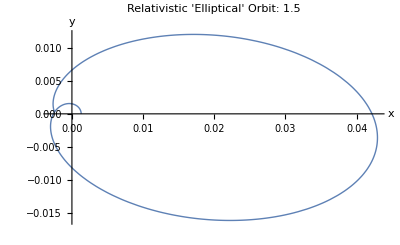

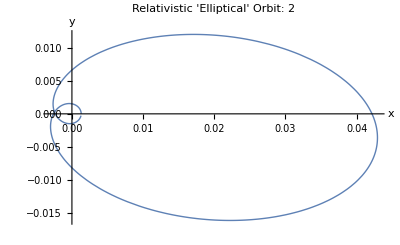

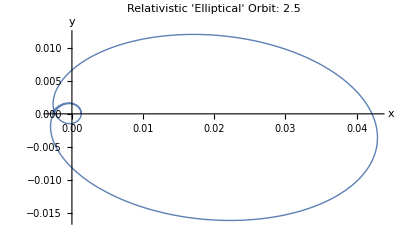

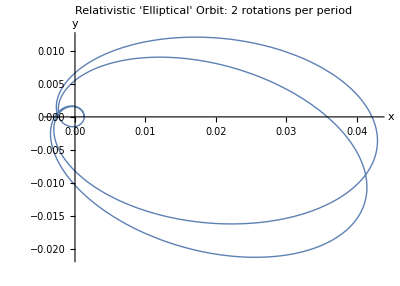

```mathematica
(*---Constants and Setup---*)(*Pretty print subscript-style variables for display only*)MakeBoxes[nt,StandardForm]:=SubscriptBox["n","t"]
MakeBoxes[nr,StandardForm]:=SubscriptBox["n","r"]

(*Physical constants*)
Z=118; (*Atomic number of Oganesson, Og*)
α=1/137.036; (*Fine structure constant*)

(*Quantum numbers*)
ntVal=1;
nrVal=1;

(*---Define symbolic formulas as functions---*)

(*Eq.(3.19)*)
ωFunc[nt_]:=Sqrt[nt^2-Z^2 α^2]/nt

(*Eq.(3.20)*)
ϵFunc[nt_,nr_]:=Sqrt[nr] Sqrt[(nr+2 Sqrt[nt^2-Z^2 α^2])]/(nr+Sqrt[nt^2-Z^2 α^2])

(*Eq.(3.21)*)
aFunc[nt_,nr_]:=((nr+Sqrt[nt^2-Z^2 α^2]) Sqrt[Z^2 α^2+(nr+Sqrt[nt^2-Z^2 α^2])^2])/Z

(*---Compute numeric values---*)

ωVal=ωFunc[ntVal]//N
ϵVal=ϵFunc[ntVal,nrVal]//N
aVal=aFunc[ntVal,nrVal]//N
{rMin=aVal*(1-ϵVal) //N, rMax=aVal*(1+ϵVal) //N}
DeltaTheta=2*Pi*((1/ωVal) -1) //N
PeriodTheta=2*Pi*(1/ωVal)  //N

(*---Define relativistic radial orbit r(t) from Eq.(3.9)---*)
r[t_]:=(aVal (1-ϵVal^2))/(1+ϵVal Cos[ωVal t])

 PolarPlot[r[t],{t,0,0.75*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 1.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.269*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2.5",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
PolarPlot[r[t],{t,0,1.75*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: 2 rotations per period",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
Export["OganessonIon117.pdf",%]
```

OganessonIon117.pdf

```mathematica
(*Animation in Cartesian Coordinates*)Manipulate[ParametricPlot[{r[t] Cos[t],r[t] Sin[t]},{t,0,tMax},PlotStyle->{Blue,Thick},AxesLabel->{"x","y"},PlotLabel->Style["Relativistic 'Elliptical Orbit'(Animated, Cartesian)",14,Bold],PlotRange->{{-rMax,rMax},{-rMax,rMax}},(*Fixed range ensures full visibility from Subscript[r, min]=0.001299 to Subscript[r, max]=0.0431087*)AspectRatio->1,PlotPoints->1000,PerformanceGoal->"Quality"],{tMax,0.01,24 Pi,Appearance->"Labeled"}]
```

Summary: 
In the above animation of the relativistic Kepler motion of an electron in hydrogen-like Oganesson ion, Og, when Z=118, the nucleus is situated  in the fixed focus at the origin.  For this quantum state, we choose n_r=nr=1 and n_θ=nt=1 in the fine structure formula (3.18). By (3.19)-(3.21), one gets: ω=0.508457,  ϵ=0.941479, and a=0.0222041, in Bohr’s atomic units. 
The perihelion and aphelion move along two concentric circles around the nucleus with radii:  r_min=a (1-ϵ)=0.0012994 and r_max=a (1+ϵ)=0.043108700, respectively.  In the animation, the geometrical loci of the successive perihelia and aphelia, the outer and inner envelopes of the orbit, see Figure 3, are not shown for simplicity.
Rotation of the ellipse over one period is given by Δθ=2π(1/ω-1)=6.07418.  At the point of self-intersection one gets, approximately,  r[3.074037420536865]=r[9.283329709624294]=0.0025044 with  r[9.283329709624294`]-r[3.074037420536865`]=4.33681×10^-19.

```mathematica
r[9.283329709624294]-r[3.074037420536865]
```

4.33681×10^-19

```mathematica
{r[9.283329709624294],r[3.074037420536865]}
```

{0.0025044,0.0025044}

```mathematica
ωVal*(9.283329709624294+3.074037420536865)/2//N
```

3.14159

```mathematica
3.141592653589793-Pi//N
```

0.

```mathematica
r0[t_]:=0.004308954533019283
```

```mathematica
r[t_]:=0.0025227511535937256/(1+0.9414793136551063 Cos[0.5084566348962754 t])
```

```mathematica
{r0[t], r[t]}
```

{0.00430895,0.00252275/(1+0.941479 Cos[0.508457 t])}

```mathematica
PeriodTheta
```

12.3574

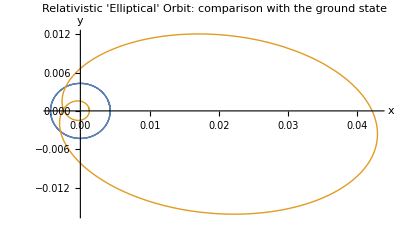

```mathematica
PolarPlot[{r0[t], r[t]},{t,0,1.05*PeriodTheta},PlotLabel->"Relativistic 'Elliptical' Orbit: comparison with the ground state",AxesLabel->{"x","y"},PlotRange->All,PlotStyle->Thick]
```

```mathematica
Export["OganessonIon117SP.pdf",%]
```

OganessonIon117SP.pdf